```mathematica
filesAR=FileNames["/home/carla//GDC/CONF/SED/GDC_Conf_AR_SED_ALL_Out/*.txt"];
dataAR=Map[Get[#]&, filesAR];
filesBR=FileNames["/home/carla//GDC/CONF/SED/GDC_Conf_BR_SED_ALL_Out/*.txt"];
dataBR=Map[Get[#]&, filesBR];
```

```mathematica
confAR=dataAR[[All,1]];
confBR=dataBR[[All,1]];
```

```mathematica
dojAR=confAR[[All,1]][[All,1]];
zAR=confAR[[All,2]][[All,1]];
fAR=confAR[[All,3]][[All,1]];
```

```mathematica
dojBR=confBR[[All,1]][[All,1]]
zBR=confBR[[All,2]][[All,1]]
fBR=confBR[[All,3]][[All,1]]
```

{0.00505051,0.00409836,0.00297619,0.00297619,0.00348432}

{0.00397958,0.00348843,0.00263474,0.0026388,0.0031497}

{0.650107,0.740913,0.79416,0.796357,0.824758}

```mathematica
sList={3,4,5,6,7,8};
sList2={3.5,4.5,5.5,6.5,7.5};
ran=Range[Length[sList]];
ran2=Range[Length[sList2]];


dojPAR={#[[2]],#[[1]]}&/@Map[{dojAR[[#]],sList[[#]]}&,ran];
zPAR= {#[[2]],#[[1]]}&/@Map[{zAR[[#]],sList[[#]]}&,ran];
fPAR= {#[[2]],#[[1]]}&/@Map[{fAR[[#]],sList[[#]]}&, ran];
dojPBR={#[[2]],#[[1]]}&/@Map[{dojBR[[#]],sList2[[#]]}&,ran2];
zPBR= {#[[2]],#[[1]]}&/@Map[{zBR[[#]],sList2[[#]]}&,ran2];
fPBR= {#[[2]],#[[1]]}&/@Map[{fBR[[#]],sList2[[#]]}&, ran2];
```

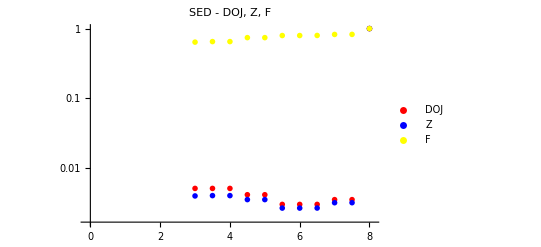

```mathematica
PlotAllParts=ListLogPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotRange->{{-0.1,8.1},All},PlotStyle-> {Red, Blue, Yellow}, PlotRange->All, PlotLabel->"SED - DOJ, Z, F", PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
```

```mathematica
SetDirectory["/home/carla//GDC/CONF/SED/"];
Put[Union[dojPAR,dojPBR],"SED_DOJ.txt"]
Put[Union[zPAR, zPBR],"SED_Z.txt"]
Put[Union[fPAR,fPBR],"SED_F.txt"]
Export["SED.jpeg",PlotAllParts,ImageSize->800, ImageResolution-> 300]
```

SED.jpeg

```mathematica
(*PlotParts=ListPlot[{Union[dojPAR,dojPBR], Union[zPAR,zPBR], Union[fPAR, fPBR]}, PlotLegends->{"DOJ","Z", "F"}, PlotStyle-> {Red, Blue, Yellow}, PlotRange->{0, 0.005},  PlotLabel->"SED - DOJ, Z, F - Zoomed In",  PlotMarkers->{{"D",12},{"Z",12},{"F",12}}]
Export["SED_Zoomed_In.jpeg",PlotParts,ImageSize->850]*)
```